#### Define the Transfer Function

TF is given by
          G(s)=1/(ms^2+cs+k)

```mathematica
(*Define the constants*)
```

```mathematica
m = 1;
c = 3;
k = 5;
(*Define the TF*)
```

```mathematica
G[s_]= 1/(m s^2+c s+k)
```

1/(5+3 s+s^2)

#### Evaluate the response due to a unit step

Recall a  unit step is given by
    u(t) = 1
    U(s)=L[u(t)]=L[1]=1/s

U[s_] =1/s;
Transfer funtion will alow to predict the response to the input

Y (s)=G(s)U(s)=1/(ms^2+cs+k)*1/s

```mathematica
Y[s_] = G[s]*U[s]
```

1/(s (5+3 s+s^2))

```mathematica
(*Use Mathematica to get this from the s domain to the time domain*)
```

```mathematica
y[t_]=InverseLaplaceTransform[Y[s],s,t]
```

1/5-(ⅇ^(-3 t/2) (√11 Cos[(√11 t)/2]+3 Sin[(√11 t)/2]))/(5 √11)

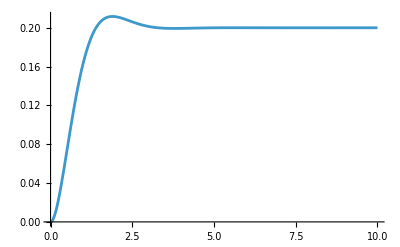

```mathematica
Plot[y[t],{t,0,10},
PlotRange->All]
```

## Evaluate response due to a sisoid

Choose input of 
         u(t)=5sin(2t)
    Get the Laplace represantion of u(t)

```mathematica
U[s_]=LaplaceTransform[5 Sin[2 t],t,s]
```

10/(4+s^2)

Output is simply Y(s)=G(s)U(s)

```mathematica
Y[s_]= G[s]*U[s]
```

10/((4+s^2) (5+3 s+s^2))

```mathematica
y[t_]=InverseLaplaceTransform[Y[s],s,t]
```

10 (1/74 (-6 Cos[2 t]+Sin[2 t])+(ⅇ^(-3 t/2) (3 √11 Cos[(√11 t)/2]+7 Sin[(√11 t)/2]))/(37 √11))

```mathematica
y[t]//Simplify
```

5/407 (11 (-6 Cos[2 t]+Sin[2 t])+2 ⅇ^(-3 t/2) (33 Cos[(√11 t)/2]+7 √11 Sin[(√11 t)/2]))

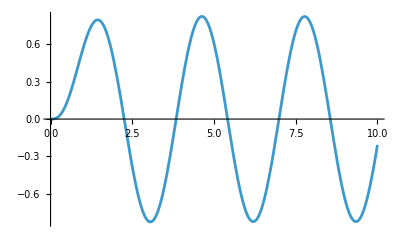

```mathematica
Plot[y[t],{t,0,10}]
```